```mathematica
imputfile=Import["Desktop/data3.csv"]
```

{{kf,m1*/m1,m2*/m2,sms/ms,smw/mw},{0.1,0.999841,0.999841,1.00001,1.},{0.2,0.998729,0.998731,1.00006,1.},{0.3,0.995718,0.995724,1.00021,1.},{0.4,0.989881,0.989895,1.0005,1.00001},{0.5,0.980332,0.980359,1.00098,1.00003},{0.6,0.96625,0.966297,1.0017,1.0001},{0.7,0.946914,0.946987,1.00269,1.00024},{0.8,0.92174,0.921847,1.00401,1.00052},{0.9,0.89033,0.89048,1.00569,1.00103},{1.,0.852517,0.85272,1.00774,1.00188},{1.1,0.808419,0.808683,1.01015,1.00322},{1.2,0.758486,0.758818,1.01286,1.00519},{1.3,0.703554,0.703962,1.01575,1.00797},{1.4,0.644897,0.645386,1.01858,1.01167},{1.5,0.584253,0.584825,1.02099,1.01637},{1.6,0.523782,0.524437,1.02243,1.02205},{1.7,0.465855,0.46659,1.02218,1.02856},{1.8,0.412618,0.413427,1.01938,1.03569},{1.9,0.365492,0.366365,1.01306,1.04325},{2.,0.324923,0.325853,1.00231,1.05109},{2.1,0.290558,0.291534,0.986208,1.05922},{2.2,0.261616,0.262633,0.963841,1.06769},{2.3,0.237232,0.238282,0.93417,1.07662},{2.4,0.216627,0.217705,0.895945,1.08612},{2.5,0.199182,0.200284,0.847548,1.09631},{2.6,0.184432,0.185555,0.786716,1.10727},{2.7,0.172047,0.173187,0.709968,1.11904},{2.8,0.161805,0.162959,0.611165,1.13164},{2.9,0.153567,0.154732,0.476774,1.14509},{3.,0.147259,0.148433,0.256143,1.15936}}

```mathematica
dataset=Dataset[imputfile]
```

Dataset[<>]

Dataset[<>]

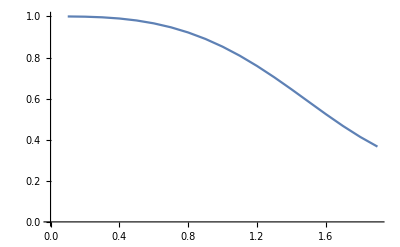

```mathematica
plotdata1=dataset[2;;20, {1, 3}]
graph1=ListLinePlot[plotdata1]
```

Dataset[<>]

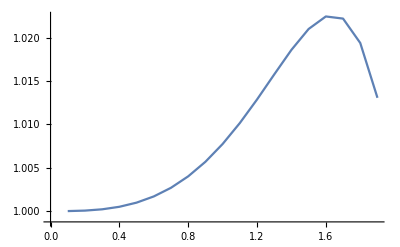

```mathematica
plotdata2=dataset[2;;20, {1, 4}]
graph2=ListLinePlot[plotdata2]
```

Dataset[<>]

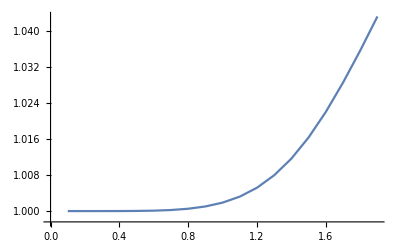

```mathematica
plotdata3=dataset[2;;20, {1, 5}]
graph3=ListLinePlot[plotdata3]
```

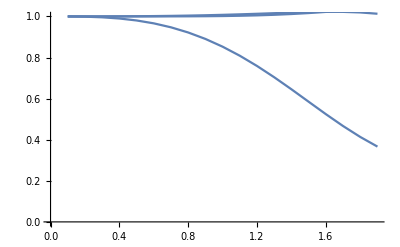

```mathematica
Show[graph1, graph2, graph3]
```